```mathematica
(*Off[SixJSymbol::tri];
Off[ThreeJSymbol::tri];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
$Assumptions=α∈Reals;*)
```

```mathematica
RootPath=NotebookDirectory[];
```

```mathematica
(* The total angular momentum quantum number is conserved, so we solve only for a specific J *)
Jz=0;
(* The full two-body energy cutoff for the basis *)
EMax=24;(*=NMax+3*)
(* Easiest to set a value of a at the beginning so that the matrix elements become numerical *)
a=-1;
(* This is needed because the eigenvalue solver finds the eigenvalues with the smallest magnitude. Choose a postive number at least the size of the most negative eigenvalue expected *)
EOffsetNOCM=0;
```

```mathematica
(* Determine the two body l=0 center of mass eigenenergies in the absence of SOC from Busch formula *)
If[a!=0,
νValues=Table[FindRoot[Sqrt[2]Gamma[-ν]/Gamma[-ν-1/2]==1/a,{ν,νGuess},AccuracyGoal->30],{νGuess,-2,(EMax/2-.75)+.25,.05*Sqrt[2]}];
νValues=DeleteDuplicates[νValues,Abs[ReplaceAll[ν,#1]-ReplaceAll[ν,#2]]<=.1&];,
νValues=Table[{ν->i},{i,0,EMax-3}] (* Handle a=0 case *);]
EValues=Sort[2ν+3/2/.νValues] ;(* List of l=0 energies under the cutoff *)
νValues=Sort[Flatten[ν/.νValues]];
```

```mathematica
(* Make sure all Busch energies are below the cutoff *)
While[2*νValues[[-1]]+3>EMax,νValues=Delete[νValues,-1]]
While[EValues[[-1]]+3/2>EMax,EValues=Delete[EValues,-1]]
```

```mathematica
(* List of Busch quantum numbers under the energy cutoff *)
νValues
```

{-0.256299,0.669483,1.63632,2.61694,3.60392,4.59444,5.58713,6.58129,7.57648,8.57243,9.56896}

```mathematica
(* List of Busch 2-body CoM Energies below the cutoff *)
EValues
```

{0.987402,2.83897,4.77264,6.73387,8.70785,10.6889,12.6743,14.6626,16.653,18.6449,20.6379}

```mathematica
(* Indexing of states *)
Clear[ni,li,Ni,Li,si,ji,Ji];
imax=0;
i=0;
verbose=False;

If[EValues[[1]]≤3/2,δEMax=EValues[[1]]-3/2,δEMax=0]; 
(* When the lowest Busch energy is less than 3/2, we can get higher N in each shell *)
For[EShell=3,EShell≤EMax,++EShell,
N0=0;L=0;
For[s=0,s≤1,++s,
For[l=0,l==0||l<=EShell-2N0-L-3,++l,
For[j=Abs[l-s],j≤l+s,++j,
J=j;
If[l==0&&s==0,
For[ii=1,ii≤Length[EValues],++ii,
If[2N0+L+3/2+EValues[[ii]]>EShell,Break];
If[(EShell-1<2N0+L+3/2+EValues[[ii]]||EShell==3)&&2N0+L+3/2+EValues[[ii]]≤EShell,
++i;++imax;
Ji[i]=J;
Jzi[i]=Jz;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=νValues[[ii]];
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J," ",Jz,">"];
Print["E=",2N0+L+3/2+2*ni[i]+3/2];](* End If[Verbose] *)
](* End If[EvenQ... ] *)
](* End ii loop *)(* End l==0 case, ν loop*),
For[n=0,2n+l+3/2+2N0+L+3/2≤EShell,++n,
If[EvenQ[l+s]&&2(N0+n)+L+l+3==EShell,
++i;++imax;
Ji[i]=J;
Jzi[i]=Jz;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=n;
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J,Jz,">"];
Print["E=",2N0+L+3/2+2ni[i]+l+3/2];](* End If[Verbose] *)
] (* End If[EvenQ...] *)
](* End For[n=0...] *)
] (* End If[l==0] *)
] (* End j loop *)
](* End l loop *)
]; (* End s loop *)
iShell[EShell]=imax;
] (* End EShell loop *)
Clear[i,ii,l,L,N0,n,s,j,J];
Print["There are a total of ",imax," ","included states."]
```

There are a total of 264 included states.

```mathematica
(* Use this to figure out the quantum nubmers of a given state *)
PrintState[i_]:=Print["|",i,">=|",ni[i],"(",li[i],si[i],")",ji[i],";",Ni[i],Li[i],";(",ji[i],Li[i],")",Ji[i],Jzi[i],">"]
```

```mathematica
(*shellSizeTableRashba=Table[{EShell,iShell[EShell]},{EShell,4,32,1}]
ListPlot[shellSizeTableRashba,Joined->True,PlotRange->{{0,32},{0,120000}},Axes->False,Frame->True,PlotLabel->"Number of states with E<=E_Max",FrameLabel->{"E_Max","Number of States"}];
ListPlot[{shellSizeTableRashba,shellSizeTableWeyl},Joined->True,PlotRange->{{0,32},{0,15000}},Axes->False,Frame->True,PlotLabel->"Number of states with E<=E_Max",FrameLabel->{"E_Max","Number of States"},PlotLegends->{"Rashba","Weyl"}]*)
```

```mathematica
(* Save all the angular momentum coupling coefficients after computing once *)
JThree[{j1_,j1m_},{j2_,j2m_},{J_,Jm_}]:=JThree[{j1,j1m},{j2,j2m},{J,Jm}]=ThreeJSymbol[{j1,j1m},{j2,j2m},{J,Jm}];
JSix[{j1_,j2_,j3_},{j4_,j5_,j6_}]:=JSix[{j1,j2,j3},{j4,j5,j6}]=SixJSymbol[{j1,j2,j3},{j4,j5,j6}];
(* 9-j symbol ({{j1, j2, j12}, {j3, j4, j34}, {j13, j24, j}})*)
JNine[{j1_,j2_,j12_},{j3_,j4_,j34_},{j13_,j24_,j_}]:=JNine[{j1,j2,j12},{j3,j4,j34},{j13,j24,j}]=Simplify[Sum[(-1)^(2g)(2g+1)JSix[{j1,j2,j12},{j34,j,g}]JSix[{j3,j4,j34},{j2,g,j24}]JSix[{j13,j24,j},{g,j1,j3}],{g,Max[Abs[j1-j],Abs[j2-j34],Abs[j3-j24]],Min[j1+j,j2+j34,j3+j24],1-Mod[2*(j1+j),2]/2}]]
```

```mathematica
(* Normalization factor for Busch wave functions. Provide a limiting definition for half-integer ν when a->+∞,-∞ *)
AbsoluteTiming[If[a≠∞&&a≠-∞,A[ν_]:=A[ν]=((Gamma[-ν] (-PolyGamma[0,-1/2-ν]+PolyGamma[0,-ν]))/(8 π^2 Gamma[-1/2-ν]))^(-1/2),
For[ν0=-1/2,ν0<=νValues[[-1]]+.01,ν0++,A[N[ν0]]=Limit[((Gamma[-ν] (-PolyGamma[0,-1/2-ν]+PolyGamma[0,-ν]))/(8 π^2 Gamma[-1/2-ν]))^(-1/2),ν->ν0]]
] (* End if *)
] (* End AbsoluteTiming *)
```

{0.00007,Null}

```mathematica
(* This is the actual reduced matrix element of Q *)
Q[n1_,l1_,n_,l_]:=Q[n1,l1,n,l]= If[Abs[l1-l]==1,(I (-1)^(l1+1))/JThree[{l1,0},{1,0},{l,0}] √(n!n1!Gamma[n+l+3/2]Gamma[n1+l1+3/2])Sum[(-1)^(m+m1)/(m!m1!(n-m)!(n1-m1)!Gamma[m+l+3/2]Gamma[m1+l1+3/2])Which[l1==l+1,(l+1)/Sqrt[(2l+1)(2l+3)] (2m Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),l1==l-1,l/Sqrt[(2l+1)(2l-1)]((2m+2l1+1) Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),True,0],{m,0,n},{m1,0,n1}],0];
(* This is the actual reduced matrix element of q, accounting for the Busch states at l=0 *)
q[n1_,l1_,n_,l_]:=q[n1,l1,n,l]=
If [l1>0&&l>0||a==0,(* Case where neither l or l1=0 *)Q[n1,l1,n,l],
If[l1==0&&l==1&&a≠0,(* Recursive definition for < ν l1=0 ||q || n l=1 > case *)q[n,1,n1,0], 
If[l1==1&&l==0&&a≠0, (* Definition for < n1 l1=1 ||q || ν l=0 > case *)
-I A[n]Sqrt[Gamma[n1+5/2]/(2 π^3 Gamma[n1+1])](-1-2 n1+2 n)/(2 (n1-n) (1+n1-n))
]
]
];
```

```mathematica
(* Matrix elements of σ.q *)
(* Note that α is not included! *)
σq[n1_,s1_,l1_,j1_,L1_,J1_,J1z_,n_,s_,l_,j_,L_,J_,Jz_]:=  N[6. I Sqrt[(2J+1)(2J1+1)(2j+1)(2j1+1)](-1)^(J+J1-J1z+j1+L+1)JThree[{J1,-J1z},{1,0},{J,Jz}]JSix[{j1,J1,L},{J,j,1}]JNine[{l1,l,1},{s1,s,1},{j1,j,1}]q[n1,l1,n,l]](s1-s)
```

```mathematica
(* Matrix σ.q+Σ.Q, stored as SparseArray *)
Print["There are a total of ",imax," ","included states."]
AbsoluteTiming[
σqΣQ=SparseArray[
Flatten[
ParallelTable[Quiet[If[Jzi[i]==Jzi[j]&&Abs[Ji[i]-1]≤Ji[j]≤Ji[i]+1&&Abs[li[i]-li[j]]==1&&Abs[si[i]-si[j]]==1&&Abs[ji[i]-1]≤ji[j]≤ji[i]+1&&Li[i]==Li[j]&&Ni[i]==Ni[j],{{i,j}->Chop[σq[ni[i],si[i],li[i],ji[i],Li[i],Ji[i],Jzi[i],ni[j],si[j],li[j],ji[j],Li[j],Ji[j],Jzi[j]]]}
,##&[]](* If ΔJ≤1 && Jz==Jz *)
](* End quiet *)
,{i,2,imax},{j,1,i-1}]
],{imax,imax}
];]
σqΣQ=SparseArray[σqΣQ+ConjugateTranspose[σqΣQ]];
```

There are a total of 264 included states.

{7.87217,Null}

```mathematica
Normal[σqΣQ][[1;;10,1;;10]]//MatrixForm
```

(0 | 0 | -1.56873 | 0 | 0 | 0 | 0 | -0.654293 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.56873 | 0 | 0 | 0 | -0.498795 | -0.816497 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.498795 | 0 | 0 | 0 | 0 | -1.94462 | 0 | 0
0 | 0 | -0.816497 | 0 | 0 | 0 | 0 | -0.516398 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.654293 | 0 | 0 | 0 | -1.94462 | -0.516398 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* Matrix of Subscript[H, HO]+Subscript[H, contact], stored as SparseArray *)
H0=SparseArray[ParallelTable[{i,i}->2ni[i]+2Ni[i]+li[i]+Li[i]+3+EOffsetNOCM,{i,1,imax}]];
```

```mathematica
Clear[DataNOCM]
αMin=0;αMax=.75;αStep=N[1/200*Sqrt[2]];
nEigValuesNOCM=12;
AbsoluteTiming[Do[EnergiesNOCM[α0]=Sort[Eigenvalues[SparseArray[H0+α0 σqΣQ],-nEigValuesNOCM]],{α0,αMin,αMax,αStep}]]
DataNOCM[j_]:=DataNOCM[j]=Table[{α,EnergiesNOCM[α][[j]]-EOffsetNOCM},{α,αMin,αMax,αStep}];
```

{0.90799,Null}

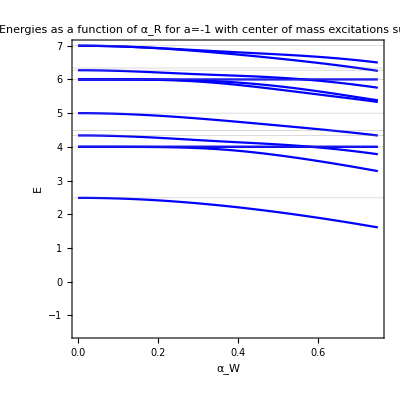

```mathematica
(* Plot of energies as a function of Subscript[α, Rashba] *)
ListPlot[Table[DataNOCM[i],{i,1,nEigValuesNOCM,1}],Joined->True,PlotRange->{{αMin,αMax},{-1.5,7}},Frame->True,FrameLabel->{"α_W","E"},PlotStyle->Directive[Blue],GridLines->{{},Join[EValues+3/2,EValues+7/2,Table[i+3,{i,1,EMax-4}]]},AspectRatio->1.0,PlotLabel->StringJoin["Energies as a function of α_R for a=",ToString[a]," with center of mass excitations suppressed"]]
```

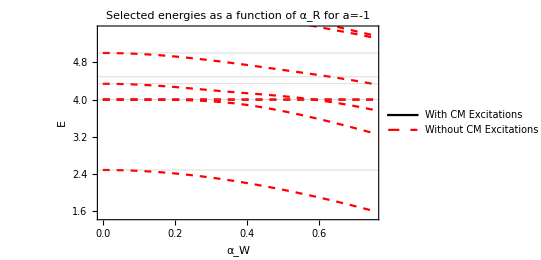

```mathematica
If[a==-1,DataWithCM=Join[{Data[1]},{Data[3]},{Data[4]},{Data[5]},{Data[6]},{Data[9]}];minE=1.5;maxE=5.5];
Fig=Show[
ListPlot[DataWithCM,Joined->True,PlotRange->{{αMin,αMax},{minE,maxE}},Frame->True,FrameLabel->{"α_W","E"},PlotStyle->Directive[Black],GridLines->{{},Join[EValues+3/2,EValues+7/2,Table[i+3,{i,1,EMax-4}]]},AspectRatio->.65,PlotLabel->StringJoin["Selected energies as a function of α_R for a=",ToString[a]],PlotLegends->{"With CM Excitations"}],
(**)
ListPlot[Table[DataNOCM[i],{i,1,nEigValuesNOCM,1}],Joined->True,PlotStyle->Directive[Red,Dashed],PlotLegends->{"Without CM Excitations"}]
]
If[a==-1,
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/NoCMa-1.eps",Fig]];
If[a==1,
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/NoCMa+1.eps",Fig]];
If[a==∞,
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/NoCMainf.eps",Fig]];
If[a==0,
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/NoCMa0.eps",Fig]];
```

```mathematica
(* Create lists of eigenvalues for different EMax *)
Clear[i];
αTest=0.5;
Convergence1={};
Convergence2={};
Convergence3={};
Convergence4={};
Convergence5={};
Convergence6={};
Convergence7={};
Convergence8={};
FullH=H0+αTest σqΣQ;
For[Emax=6,Emax≤EMax,Emax+=2,
H=Chop[N[SparseArray[FullH[[1;;iShell[Emax],1;;iShell[Emax]]]]]];
EList=Eigenvalues[H,-8]-EOffsetNOCM;
AppendTo[Convergence1,{Emax,EList[[-1]]}];AppendTo[Convergence2,{Emax,EList[[-2]]}];
AppendTo[Convergence3,{Emax,EList[[-3]]}];AppendTo[Convergence4,{Emax,EList[[-4]]}];
AppendTo[Convergence5,{Emax,EList[[-5]]}];AppendTo[Convergence6,{Emax,EList[[-6]]}];
AppendTo[Convergence7,{Emax,EList[[-7]]}];AppendTo[Convergence8,{Emax,EList[[-8]]}];]
```

```mathematica
(* Fractional convergence of eigenvalues at EMax compared to EMax-2 *)
conv[Convergence_]:=Abs[(Convergence[[-1,2]]-Convergence[[-2,2]])/Convergence[[-2,2]]];
conv[Convergence1]
conv[Convergence2]
conv[Convergence3]
conv[Convergence4]
conv[Convergence5]
conv[Convergence6]
conv[Convergence7]
conv[Convergence8]
```

0.000613056

0.000129162

2.22045×10^-16

2.22045×10^-16

0.000284951

6.5977×10^-6

0.0000885694

0.0000182235

```mathematica
MemoryInUse[]/10^6//N
MaxMemoryUsed[]/10^6//N
```

56.8691

57.4602

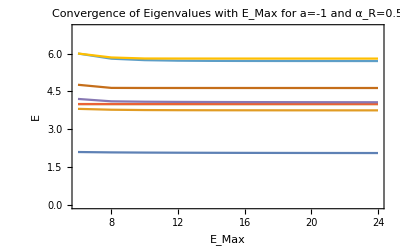

```mathematica
(* Make convergence plots *)
ListPlot[{Convergence1,Convergence2,Convergence3,Convergence4,Convergence5,Convergence6,Convergence7,Convergence8},Joined->True,Axes->False,Frame->True,PlotRange->{{6,EMax},{0,7}},PlotLabel->StringJoin["Convergence of Eigenvalues with E_Max for a=", ToString[a]," and α_R=",ToString[αTest]],FrameLabel->{"E_Max","E"}]
```

```mathematica
(* Create lists of eigenvalues for different EMax *)
Clear[i];
αTest=.05;
Convergence1={};Convergence2={};Convergence3={};Convergence4={};
Convergence5={};Convergence6={};Convergence7={};Convergence8={};
FullH=H0+αTest σqΣQ;
For[Emax=6,Emax≤EMax,Emax+=2,
H=Chop[N[SparseArray[FullH[[1;;iShell[Emax],1;;iShell[Emax]]]]]];
EList=Eigenvalues[H,-8]-EOffsetNOCM;
AppendTo[Convergence1,{Emax,EList[[-1]]}];AppendTo[Convergence2,{Emax,EList[[-2]]}];
AppendTo[Convergence3,{Emax,EList[[-3]]}];AppendTo[Convergence4,{Emax,EList[[-4]]}];
AppendTo[Convergence5,{Emax,EList[[-5]]}];AppendTo[Convergence6,{Emax,EList[[-6]]}];
AppendTo[Convergence7,{Emax,EList[[-7]]}];AppendTo[Convergence8,{Emax,EList[[-8]]}];]
```

```mathematica
(* Fractional convergence of eigenvalues at EMax compared to EMax-2 *)
conv[Convergence_]:=Abs[(Convergence[[-1,2]]-Convergence[[-2,2]])/Convergence[[-2,2]]];
conv[Convergence1]
conv[Convergence2]
conv[Convergence3]
conv[Convergence4]
conv[Convergence5]
conv[Convergence6]
conv[Convergence7]
conv[Convergence8]
```

5.13866×10^-6

8.97268×10^-8

1.9984×10^-15

1.33227×10^-15

3.67052×10^-6

1.76693×10^-12

1.57796×10^-7

5.49206×10^-8

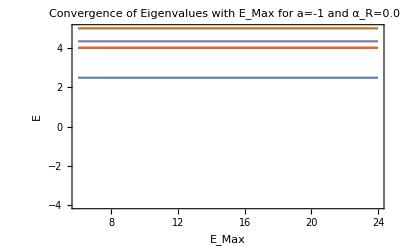

```mathematica
(* Make convergence plots *)
ListPlot[{Convergence1,Convergence2,Convergence3,Convergence4,Convergence5,Convergence6,Convergence7,Convergence8},Joined->True,Axes->False,Frame->True,PlotRange->{{6,EMax},{-4,5}},PlotLabel->StringJoin["Convergence of Eigenvalues with E_Max for a=", ToString[a]," and α_R=",ToString[αTest]],FrameLabel->{"E_Max","E"}]
```

```mathematica
MemoryInUse[]/10^6//N
MaxMemoryUsed[]/10^6//N
```

57.1016

57.5252

```mathematica
(* This gives the second derivative of Data wrt α at α=0 *) 
E2[Data_,n_]:=(2*Data[[1+n,2]]-2*Data[[1,2]])/(Data[[1+n,1]])^2
Table[E2[DataNOCM[1],n],{n,1,11,2}]
```

{-3.79536,-3.79447,-3.79269,-3.79003,-3.7865,-3.78212}

```mathematica
If[EMax==24,
If[a==-1,Export[FileNameJoin[{RootPath,"Saved","RNoCMam1.m"}],Table[DataNOCM[i],{i,1,nEigValuesNOCM}]]
];
]
```